```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[1,0.0001,1,0]
```

2.99292

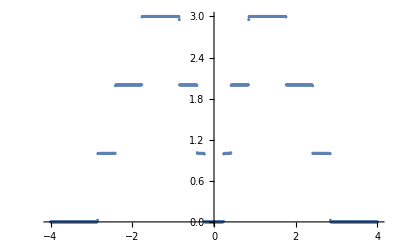

```mathematica
ListPlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[-4,4,0.01]}]]
```

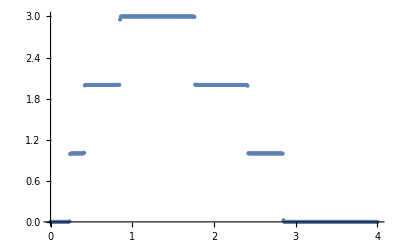

```mathematica
ListPlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,4,0.01]}]]
```

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{i=RandomInteger[{1,14}]},Inverse[β[ω,δ,t,ϵ]-ReplacePart[β[0,0,0,0],{{i,i}}->ϵ1]]]
```

```mathematica
imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{i=RandomInteger[{1,7}],j=RandomInteger[{8,14}]},Inverse[β[ω,δ,t,ϵ]-ReplacePart[β[0,0,0,0],{{i,i},{j,j}}->ϵ1]]]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{i=RandomInteger[{1,7}],j=RandomInteger[{8,14}]},Inverse[β[ω,δ,t,ϵ]-ReplacePart[β[0,0,0,0],{{i,i},{j,j}}->0]]]
```

```mathematica
RandomSample[Join[Table[imp1[ω,δ,t,ϵ,ϵ1],31],Table[imp2[ω,δ,t,ϵ,ϵ1],9],Table[imp[ω,δ,t,ϵ,ϵ1],60]]]
```

{imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1]}

```mathematica
tra[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1]},list={RandomSample[{imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1]}]};b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b]
```

```mathematica
Mean[Table[tra[1 ,0.0001,1,0,0.5],5000]]
```

1.39518

```mathematica
Table[{ω,Mean[Table[tra[ω ,0.0001,1,0,0.5],5000]]},{ω,0,4,0.01}]
```

{{0.,0.0000354455},{0.01,0.0000272559},{0.02,0.0000293443},{0.03,0.0000349635},{0.04,0.0000455485},{0.05,0.0000498355},{0.06,0.0000728297},{0.07,0.0000937984},{0.08,0.000115873},{0.09,0.000155034},{0.1,0.000196078},{0.11,0.000274076},{0.12,0.000346097},{0.13,0.000415206},{0.14,0.000515838},{0.15,0.000685419},{0.16,0.000911443},{0.17,0.00111647},{0.18,0.00153137},{0.19,0.00210645},{0.2,0.0028661},{0.21,0.00439956},{0.22,0.00685556},{0.23,0.0157438},{0.24,0.0612651},{0.25,0.1272},{0.26,0.20777},{0.27,0.282749},{0.28,0.364184},{0.29,0.425477},{0.3,0.467049},{0.31,0.497254},{0.32,0.527882},{0.33,0.553889},{0.34,0.564035},{0.35,0.579355},{0.36,0.587591},{0.37,0.592613},{0.38,0.599461},{0.39,0.593382},{0.4,0.57898},{0.41,0.529575},{0.42,0.637428},{0.43,0.917588},{0.44,0.767171},{0.45,0.678951},{0.46,0.608762},{0.47,0.619061},{0.48,0.650401},{0.49,0.678574},{0.5,0.722982},{0.51,0.770688},{0.52,0.800144},{0.53,0.829026},{0.54,0.85842},{0.55,0.906986},{0.56,0.92494},{0.57,0.959738},{0.58,0.982003},{0.59,0.980059},{0.6,1.0154},{0.61,1.05066},{0.62,1.05129},{0.63,1.05808},{0.64,1.08134},{0.65,1.10148},{0.66,1.11622},{0.67,1.12127},{0.68,1.12967},{0.69,1.14487},{0.7,1.14414},{0.71,1.16098},{0.72,1.16126},{0.73,1.17135},{0.74,1.20976},{0.75,1.18441},{0.76,1.2035},{0.77,1.1959},{0.78,1.22367},{0.79,1.22488},{0.8,1.24194},{0.81,1.22837},{0.82,1.22809},{0.83,1.21767},{0.84,1.16198},{0.85,0.844104},{0.86,0.926001},{0.87,0.839627},{0.88,0.739602},{0.89,0.703094},{0.9,0.748607},{0.91,0.825226},{0.92,0.896143},{0.93,0.969336},{0.94,1.04169},{0.95,1.1111},{0.96,1.17476},{0.97,1.23922},{0.98,1.30764},{0.99,1.33928},{1.,1.38407},{1.01,1.48572},{1.02,1.40343},{1.03,1.19826},{1.04,0.776187},{1.05,0.387339},{1.06,0.331716},{1.07,0.334038},{1.08,0.329085},{1.09,0.340168},{1.1,0.375494},{1.11,0.403368},{1.12,0.417579},{1.13,0.422093},{1.14,0.449272},{1.15,0.500302},{1.16,0.598718},{1.17,0.646886},{1.18,0.712628},{1.19,0.766466},{1.2,0.814731},{1.21,0.823511},{1.22,0.884541},{1.23,0.912558},{1.24,0.880258},{1.25,0.922612},{1.26,0.958819},{1.27,0.938524},{1.28,0.95508},{1.29,0.944775},{1.3,0.973233},{1.31,0.987027},{1.32,0.962243},{1.33,1.01228},{1.34,0.971385},{1.35,1.01282},{1.36,1.0248},{1.37,1.03612},{1.38,1.03154},{1.39,0.986416},{1.4,0.992381},{1.41,1.00572},{1.42,0.972958},{1.43,0.986043},{1.44,0.99703},{1.45,0.939654},{1.46,0.945379},{1.47,0.959244},{1.48,0.95435},{1.49,0.967663},{1.5,0.961989},{1.51,0.943875},{1.52,0.929402},{1.53,0.92105},{1.54,0.895446},{1.55,0.882572},{1.56,0.851541},{1.57,0.824415},{1.58,0.795276},{1.59,0.761547},{1.6,0.740299},{1.61,0.721602},{1.62,0.719952},{1.63,0.704601},{1.64,0.691735},{1.65,0.664713},{1.66,0.620635},{1.67,0.574466},{1.68,0.562061},{1.69,0.562465},{1.7,0.549964},{1.71,0.530169},{1.72,0.593777},{1.73,0.615402},{1.74,0.708302},{1.75,0.997475},{1.76,1.57188},{1.77,1.59057},{1.78,1.35558},{1.79,1.0645},{1.8,0.807957},{1.81,0.648963},{1.82,0.543917},{1.83,0.552507},{1.84,0.590695},{1.85,0.65253},{1.86,0.71875},{1.87,0.752211},{1.88,0.798425},{1.89,0.835845},{1.9,0.859321},{1.91,0.86388},{1.92,0.875946},{1.93,0.886672},{1.94,0.898441},{1.95,0.904305},{1.96,0.904437},{1.97,0.891501},{1.98,0.889876},{1.99,0.902144},{2.,0.910678},{2.01,0.899318},{2.02,0.887248},{2.03,0.889441},{2.04,0.895039},{2.05,0.883504},{2.06,0.889698},{2.07,0.88473},{2.08,0.860748},{2.09,0.865555},{2.1,0.849671},{2.11,0.841389},{2.12,0.844913},{2.13,0.826957},{2.14,0.817504},{2.15,0.812592},{2.16,0.808769},{2.17,0.802779},{2.18,0.78698},{2.19,0.759168},{2.2,0.749161},{2.21,0.74314},{2.22,0.714574},{2.23,0.705472},{2.24,0.703861},{2.25,0.666777},{2.26,0.663202},{2.27,0.621471},{2.28,0.604358},{2.29,0.598294},{2.3,0.563167},{2.31,0.543162},{2.32,0.515594},{2.33,0.481475},{2.34,0.461611},{2.35,0.442904},{2.36,0.415085},{2.37,0.405081},{2.38,0.387928},{2.39,0.420915},{2.4,0.487415},{2.41,0.878581},{2.42,1.12744},{2.43,0.934747},{2.44,0.722894},{2.45,0.520605},{2.46,0.376778},{2.47,0.308363},{2.48,0.304549},{2.49,0.329757},{2.5,0.370766},{2.51,0.393869},{2.52,0.414777},{2.53,0.418521},{2.54,0.421271},{2.55,0.427307},{2.56,0.424876},{2.57,0.426474},{2.58,0.424043},{2.59,0.416162},{2.6,0.418318},{2.61,0.403718},{2.62,0.402306},{2.63,0.391829},{2.64,0.384236},{2.65,0.380512},{2.66,0.373451},{2.67,0.353097},{2.68,0.34661},{2.69,0.345124},{2.7,0.314053},{2.71,0.306773},{2.72,0.297551},{2.73,0.283484},{2.74,0.265351},{2.75,0.250577},{2.76,0.227121},{2.77,0.213382},{2.78,0.198314},{2.79,0.180665},{2.8,0.165752},{2.81,0.155367},{2.82,0.133143},{2.83,0.122836},{2.84,0.124288},{2.85,0.185218},{2.86,0.219314},{2.87,0.155762},{2.88,0.100877},{2.89,0.0563053},{2.9,0.0308362},{2.91,0.0145952},{2.92,0.0064168},{2.93,0.00300952},{2.94,0.00207688},{2.95,0.00144207},{2.96,0.00111411},{2.97,0.000903052},{2.98,0.000682997},{2.99,0.000594212},{3.,0.000507626},{3.01,0.000419347},{3.02,0.000345211},{3.03,0.00030406},{3.04,0.000296539},{3.05,0.000239449},{3.06,0.000201688},{3.07,0.000182583},{3.08,0.000160908},{3.09,0.000145997},{3.1,0.000133064},{3.11,0.00011721},{3.12,0.000101101},{3.13,0.0000908566},{3.14,0.0000826342},{3.15,0.0000800647},{3.16,0.0000654453},{3.17,0.000062297},{3.18,0.0000544677},{3.19,0.0000462537},{3.2,0.0000451488},{3.21,0.0000454224},{3.22,0.0000359347},{3.23,0.0000361014},{3.24,0.0000338041},{3.25,0.0000301972},{3.26,0.0000274477},{3.27,0.0000245268},{3.28,0.0000237617},{3.29,0.0000227423},{3.3,0.0000203445},{3.31,0.0000182242},{3.32,0.0000166189},{3.33,0.000017663},{3.34,0.0000153511},{3.35,0.0000143915},{3.36,0.0000127612},{3.37,0.0000129757},{3.38,0.0000121933},{3.39,0.0000113641},{3.4,0.0000106976},{3.41,9.54508×10^-6},{3.42,9.09788×10^-6},{3.43,8.87064×10^-6},{3.44,7.43478×10^-6},{3.45,8.51929×10^-6},{3.46,7.28852×10^-6},{3.47,7.10852×10^-6},{3.48,6.78793×10^-6},{3.49,5.90031×10^-6},{3.5,5.74524×10^-6},{3.51,5.60487×10^-6},{3.52,5.11483×10^-6},{3.53,4.90758×10^-6},{3.54,4.70873×10^-6},{3.55,4.04324×10^-6},{3.56,4.18869×10^-6},{3.57,3.54914×10^-6},{3.58,3.72322×10^-6},{3.59,3.58483×10^-6},{3.6,3.13332×10^-6},{3.61,3.05412×10^-6},{3.62,3.06534×10^-6},{3.63,2.77616×10^-6},{3.64,2.74854×10^-6},{3.65,2.82699×10^-6},{3.66,2.44635×10^-6},{3.67,2.37244×10^-6},{3.68,2.37474×10^-6},{3.69,2.11765×10^-6},{3.7,2.04461×10^-6},{3.71,1.90912×10^-6},{3.72,1.87668×10^-6},{3.73,1.72201×10^-6},{3.74,1.58682×10^-6},{3.75,1.65131×10^-6},{3.76,1.58744×10^-6},{3.77,1.66821×10^-6},{3.78,1.48021×10^-6},{3.79,1.35739×10^-6},{3.8,1.17051×10^-6},{3.81,1.27835×10^-6},{3.82,1.18663×10^-6},{3.83,1.12888×10^-6},{3.84,1.1687×10^-6},{3.85,1.13491×10^-6},{3.86,9.93529×10^-7},{3.87,9.75092×10^-7},{3.88,8.92369×10^-7},{3.89,8.96595×10^-7},{3.9,8.57634×10^-7},{3.91,8.40924×10^-7},{3.92,7.55714×10^-7},{3.93,7.86221×10^-7},{3.94,7.01524×10^-7},{3.95,7.09189×10^-7},{3.96,6.79466×10^-7},{3.97,6.78028×10^-7},{3.98,5.94679×10^-7},{3.99,6.12447×10^-7},{4.,5.84853×10^-7}}

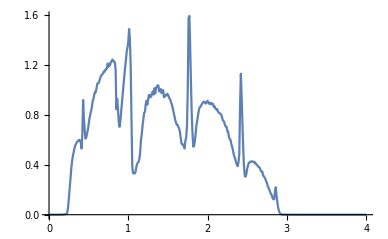

```mathematica
ListPlot[%56,Joined->True]
```

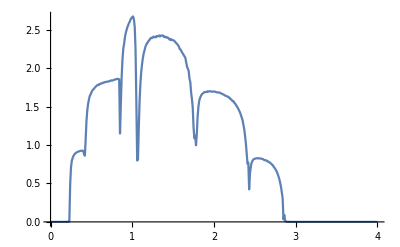

```mathematica
ListPlot[%41,Joined->True]
```

```mathematica
Export["7imp100.dat",%41]
```

7imp100.dat

```mathematica
tra2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1]},list={RandomSample[{imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp[ω,δ,t,ϵ,0],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp[ω,δ,t,ϵ,0],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1]}]};b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b]
```

```mathematica
Export["126imp100.csv",Table[{ω,Mean[Table[tra2[ω,0.0001,1,0,0.5],5000]]},{ω,0,4,0.01}]]
```

126imp100.csv

```mathematica
tra3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1]},list={RandomSample[{imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1]}]};b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b]
```

```mathematica
Export["140imp100.csv",Table[{ω,Mean[Table[tra3[ω,0.0001,1,0,0.5],5000]]},{ω,0,4,0.01}]]
```

140imp100.csv

```mathematica
tra4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1]},list={RandomSample[{imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1]}]};b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b]
```

```mathematica
Export["156imp100.csv",Table[{ω,Mean[Table[tra4[ω,0.0001,1,0,0.5],5000]]},{ω,0,4,0.01}]]
```

156imp100.csv

```mathematica
Clear[imp1,imp2,imp]
```

```mathematica
Tally[{imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp[ω,δ,t,ϵ,0],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp[ω,δ,t,ϵ,0],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,0],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1]}]
```

{{imp2[ω,δ,t,ϵ,ϵ1],40},{imp[ω,δ,t,ϵ,0],14},{imp1[ω,δ,t,ϵ,ϵ1],46}}